```mathematica
dataQ = {{0,31.415926535897874},{0.01, 31.41832339486044},{0.02,31.4207215414231},{0.03,31.423120632898538},{0.04,31.425521080509103},{0.05,31.427923230072782},{0.07,31.432733636444556},{0.1,31.65857326551975}}
```

{{0,31.4159},{0.01,31.4183},{0.02,31.4207},{0.03,31.4231},{0.04,31.4255},{0.05,31.4279},{0.07,31.4327},{0.1,31.6586}}

```mathematica
Dimensions[dataQ][[1]]
```

8

```mathematica
dataDeltaQ = Table[{dataQ [[i]][[1]],dataQ [[i]][[2]] - dataQ [[1]][[2]]},{i,1,Dimensions[dataQ][[1]]-1}]
```

{{0,0.},{0.01,0.00239686},{0.02,0.00479501},{0.03,0.0071941},{0.04,0.00959454},{0.05,0.0119967},{0.07,0.0168071}}

```mathematica
SlopeOfdeltaQvsPhi = D[Fit[dataDeltaQ,{x},x],x]
```

0.239981

```mathematica
PercentageOfactual = (SlopeOfdeltaQvsPhi/0.25)*100
```

95.9925

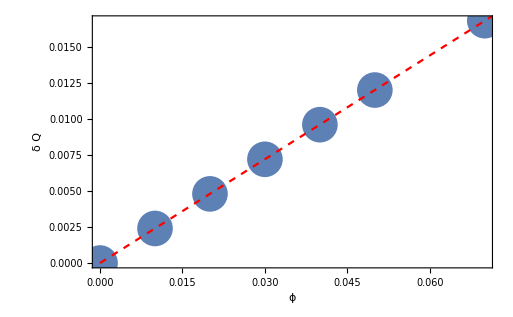

```mathematica
Show[ListPlot[dataDeltaQ,PlotStyle->PointSize[0.05]],Plot[SlopeOfdeltaQvsPhi x,{x,0,0.1},PlotStyle->{Dashed,Red}],Frame->True,BaseStyle->18,FrameStyle->{{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},FrameLabel->{  ϕ,δ Q}]
```